```mathematica
(* Normalise data *)
fileName ="laser_cont";
data =Import["C:\\p\\ann\\ex5\\"<>fileName<>".txt","CSV"];
dataT = Transpose[data];
 means=Mean/@ dataT;
sdevs = StandardDeviation/@dataT;

changeElem[x_, index_] := ((x-means[[index]])/sdevs[[index]]);
 changeRow[x_]:=(MapIndexed[changeElem,  x]); 
data = changeRow/@ data;
dataDone = N[data[[All, 1;;]]];

Export[fileName<>".csv",dataDone]
```

laser_cont.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["laser_cont.csv"]]]
```

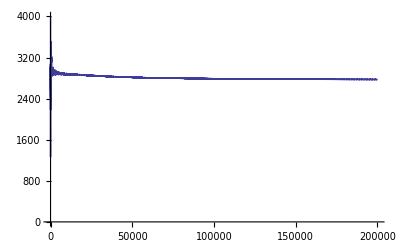

```mathematica
energy = ReadList["C:\\pg\\ffr135-ex5\energy.txt", {Number, Number}];ListLinePlot[energy[[1;;200000]], AxesOrigin->{0,0}, PlotRange->{0,4000}]
```

```mathematica
weights = Import["C:\\pg\\ffr135-ex5\weights.csv"]
weightsT = Transpose[weights];
```

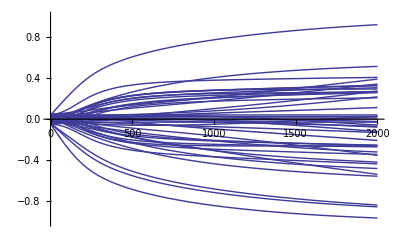

```mathematica
plots = ListLinePlot[#, AxesOrigin->{0,0}, PlotRange->{-1, 1}]&/@weightsT;
Show@@plots
```